Mathematica notebook to calculate one-loop dijet cross section (Sterman, Weinberg ‘77) at the e+ e- collider.

The one-loop corrections from the different sectors are given by [10.1103/PhysRevLett.116.192001]

-Graphics-

```mathematica
Quit[]
```

HypExp is used to expand the Hypergeometry functions

```mathematica
<<HypExp`;
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>.

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>.

Table of MZVs loaded up to weight 5

Get::noopen: Cannot open /Users/shaodingyu/lib/HPL/HPLatI1.m.

Table of values at I loaded up to weight 1

Get::noopen: Cannot open /Users/shaodingyu/lib/HPL/nmzv.m.

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1:{___,SeriesData[ϵ_,0,_,m:0|1,n_,1],___},mm2___List,x_] is Protected.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1___List,mm2:{___,SeriesData[ϵ_,0,_,m:0|1,n_,1],___},x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

## QCD Matrix element

In this section I show how to expand the full QCD amplitude (q qbar + g) in soft and collinear limit. 
In the soft limit one assumes: k^μ ~ (λ^2, λ^2, λ^2). Then the full QCD cross section = Born*soft function
In the collinear limit one assumes: k^μ & p1^μ ~ (λ^2, 1, λ) ;  p2^μ~(1,λ^2,λ). Then the full QCD cross section = Born*collinear function

```mathematica
me0sq=4(1-ϵ)e^2 μ^(2ϵ)Nc Q^2 eq^2;
```

```mathematica
me1sq=8(e eq gs μ^(2ϵ))^2 CF Nc(1-ϵ)(x1^2+x2^2-ϵ x3^2)/((1-x1)(1-x2))/.{x1->1-(2p2Dk)/Q^2,x2->1-(2p1Dk)/Q^2,x3->1-(2p1Dp2)/Q^2};
```

```mathematica
real1=me1sq/me0sq//Simplify
```

(CF gs^2 Q^2 ((1-(2 p1Dk)/Q^2)^2+(1-(2 p2Dk)/Q^2)^2-(1-(2 p1Dp2)/Q^2)^2 ϵ) μ^(2 ϵ))/(2 p1Dk p2Dk)

### soft limit

p1 = Q/2 n^μ;  p2 = Q/2(n̄)^μ

p1Dp2 = p1 . p2 ...

```mathematica
softexp={p1Dp2->Q^2/2,p1Dk->Q/2 kp λ^2,p2Dk->Q/2 km λ^2}
```

{p1Dp2→Q^2/2,p1Dk→1/2 kp Q λ^2,p2Dk→1/2 km Q λ^2}

```mathematica
real1/.softexp;
Series[%,{λ,0,-4}]//Normal;
%/.λ->1
```

(4 CF gs^2 μ^(2 ϵ))/(km kp)

### collinear limit

In the collinear limit, the three body phase space integration can be factorized as the product of the two-body part and the gluon part, as shown in (2.28) in the following note [DOI: 10.1103/PhysRevD.65.094032]. Please pay attention to the factor “p450/p40” that is always included in the collinear matrix element.

-Graphics-

```mathematica
collexp={p1Dp2->(p1m p2p)/2,p2Dk->(km p2p)/2,p1Dk->λ^2 p1Dk}
```

{p1Dp2→(p1m p2p)/2,p2Dk→(km p2p)/2,p1Dk→p1Dk λ^2}

```mathematica
real1((Q/2)/(p1m/2))/.collexp;
Series[%,{λ,0,-2}]//Normal//Expand;
%/.p2p->Q/.Q->km+p1m/.ϵ->1-ϵb//Simplify;
%/.λ->1
```

(CF gs^2 (2 km p1m+2 p1m^2+km^2 ϵb) μ^(2-2 ϵb))/(km p1Dk p1m)

#### backup (cross check with ChengTai Tan)

```mathematica
real1/((CF gs^2 Q^2 μ^(2 ϵ))/(2 p1Dk p2Dk))//Expand
```

2+(4 p1Dk^2)/Q^4+(4 p2Dk^2)/Q^4-(4 p1Dk)/Q^2-(4 p2Dk)/Q^2-ϵ-(4 p1Dp2^2 ϵ)/Q^4+(4 p1Dp2 ϵ)/Q^2

```mathematica
%39/.p1m->z Q/.p1Dp2->z Q^2/2/.p2Dk->Q^2/2(1-z)/.p1Dk->λ^2 kT^2/(2z(1-z));
Series[%,{λ,0,0}]//Normal;
%/.λ->1;
Collect[%,z]
```

%39

```mathematica
((CF gs^2 Q^2 μ^(2 ϵ))/(2 p1Dk p2Dk))/.p1m->z Q/.p1Dp2->z Q^2/2/.p2Dk->Q^2/2(1-z)
```

(CF gs^2 μ^(2 ϵ))/(p1Dk (1-z))

```mathematica
real1((Q/2)/(p1m/2))/.p1m->z Q/.p1Dp2->z Q^2/2/.p2Dk->Q^2/2(1-z)/.p1Dk->λ^2 kT^2/(2z(1-z));
Series[%,{λ,0,-2}]//Normal;
%/.λ->1;
%/(2CF gs^2 μ^(2ϵ)/kT^2);
Collect[%,z]
```

1+z^2 (1-ϵ)-ϵ+2 z ϵ

## NLO Soft Function

```mathematica
NLOsoftAmp=(4CF gs0^2)/(k3m k3p);
```

### Notation

```mathematica
Ome[n_]:=(2π^((n+1)/2))/Gamma[(n+1)/2]
```

```mathematica
mea3=1/2 1/(2π)^(d-1)1/2 k3T^(-2ϵ)Ome[1-2ϵ];
```

```mathematica
monre={k3T->√(k3p k3m),k1m->Q-k3m,k1T->k3T,k1p->k1T^2/k1m}
```

{k3T→√(k3m k3p),k1m→Q-k3m,k1T→k3T,k1p→k1T^2/k1m}

```mathematica
Variables[NLOJFun]
```

{CF,gs0,k3T,Q,d,k3m}

### Phase Space constrain

```mathematica
Oldvars={k3p,k3m}
```

{k3p,k3m}

```mathematica
paramS={k3p->Q β(1-x)y,k3m->Q β x};
```

```mathematica
constrS= UnitStep[Q β-(k3m+k3p)] //.monre
```

-k3m-k3p+β Q

```mathematica
constrS/.paramS/.UnitStep[x__]:>UnitStep[Factor[x]]
```

β Q (x-1) (y-1)

```mathematica
And@@Join[{Q>0,β>0},{0<k3m ,0<k3p}/.paramS,{constrS//.paramS/.UnitStep[x__]:>Factor[x]>0}];
Reduce[%,{x,y}]
```

β>0∧Q>0∧0<x<1∧0<y<1

```mathematica
Oldvars/.paramS
```

{β Q (1-x) y,β Q x}

```mathematica
vars={x,y};
```

```mathematica
jacoS=-Det[Table[D[Oldvars/.paramS,vars⟦i⟧],{i,1,Length[vars]}]]//Simplify
```

β^2 (-Q^2) (x-1)

### Integration

```mathematica
NLOSFun01= NLOsoftAmp mea3/.SPre/.d->4-2ϵ /.gs0->√(4π αs((μ^2 Exp[EulerGamma])/(4 π))^ϵ)//Simplify
```

(αs CF ⅇ^(ℽ ϵ) k3T^(-2 ϵ) (μ^2)^ϵ)/(π k3m k3p 1-ϵ)

```mathematica
prefac=-(ⅇ^(EulerGamma ϵ)  (μ^2)^ϵ Q^(-2 ϵ)β^(-2 ϵ))/(8  π^2 Gamma[1-ϵ])8π αs CF;
```

```mathematica
NLOSFun02=(NLOSFun01/prefac)jacoS//.monre//.paramS//PowerExpand//Simplify
```

-(1-x)^-ϵ x^(-ϵ-1) y^(-ϵ-1)

```mathematica
NLOSFun03=Integrate[NLOSFun02,{y,0,1},GenerateConditions->False]
```

((1-x)^-ϵ x^(-ϵ-1))/ϵ

```mathematica
NLOSFun04=Integrate[NLOSFun03,{x,0,1},GenerateConditions->False]
```

(1-ϵ -ϵ)/(ϵ 1-2 ϵ)

```mathematica
NLOSFun04 prefac;
Series[%/(CF αs/(4π)(μ^2/(Q^2 β^2))^ϵ)//PowerExpand,{ϵ,0,2}]//Normal;
Collect[%//FunctionExpand,ϵ,Simplify]/.Log[a_?NumberQ]:>Log[2](Log[a]/Log[2]//FullSimplify)
```

-(28 3 ϵ)/3-1/24 π^4 ϵ^2+4/ϵ^2-π^2

## NLO Jet function

```mathematica
SPre={k1Dk3:>1/2 (k1m k3p+k1p k3m)-k1T k3T Cos[π]}
```

{k1Dk3:>1/2 (k1m k3p+k1p k3m)-k1T k3T Cos[π]}

```mathematica
monre={k3p->k3T^2/k3m,k1m->Q-k3m,k1T->k3T,k1p->k1T^2/k1m}
```

{k3p→k3T^2/k3m,k1m→-k3m+Q,k1T→k3T,k1p→k1T^2/k1m}

```mathematica
NLOJFun=(4 k1m^2+4 k1m k3m+(-2+d) k3m^2)/(2 k1Dk3 k1m k3m)CF gs0^2//.SPre//.monre//Simplify
```

(CF gs0^2 ((-2+d) k3m^2-4 k3m Q+4 Q^2))/(k3T^2 Q^2)

```mathematica
NLOJFun/.k3m->(1-z)Q//Simplify
```

(CF gs0^2 (d (-1+z)^2-2 (1-4 z+z^2)))/k3T^2

```mathematica
constrC=UnitStep[δ^2-k3p/k3m] UnitStep[δ^2-k1p/k1m]//.monre
```

UnitStep[-k3T^2/k3m^2+δ^2] UnitStep[-k3T^2/(-k3m+Q)^2+δ^2]

```mathematica
Ome[n_]:=(2 π^((n+1)/2))/Gamma[(n+1)/2]
```

```mathematica
mea3=Ome[1-2 ϵ]/(2 (2 π)^(d-1))k3T^(1-2ϵ)/k3m;
```

### Phase Space constrain

```mathematica
Oldvars={k3m,k3T}
```

{k3m,k3T}

```mathematica
paramC={k3T->k3T,k3m->Q z};
```

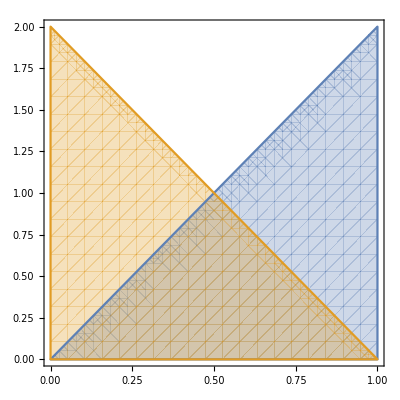

```mathematica
List@@(constrC//.paramC/.UnitStep[x__]:>x>0)/.Q->10/.δ->0.2;
RegionPlot[%,{z,0,1},{k3T,0,2}]
```

```mathematica
And@@Join[{Q>0,β>0,δ>0,z>0},{0<k3m<Q,0<k3T}/.paramC,List@@(constrC//.paramC/.UnitStep[x__]:>x>0)];
Reduce[%,{k3T,z}]
```

β>0&&δ>0&&Q>0&&0<k3T<(Q δ)/2&&k3T/(Q δ)<z<(-k3T+Q δ)/(Q δ)

```mathematica
Oldvars/.paramC
```

{Q z,k3T}

```mathematica
vars={k3T,z};
```

```mathematica
jacoC=-Det[Table[D[(Oldvars/.paramC), vars⟦i⟧],{i,1,Length[vars]}]]//Simplify
```

Q

### Integration

```mathematica
NLOJFun01=Simplify[PowerExpand[NLOJFun mea3/.SPre/.d->4-2 ϵ/.gs0->√(4π αs((μ^2 Exp[EulerGamma])/(4 π))^ϵ)]]
```

-(CF ⅇ^(EulerGamma ϵ) k3T^(-1-2 ϵ) αs (2 k3m Q-2 Q^2+k3m^2 (-1+ϵ)) μ^(2 ϵ))/(k3m π Q^2 Gamma[1-ϵ])

```mathematica
NLOJFun01 Q/.k3m->Q z/.k3T->kT//Simplify
```

-(CF ⅇ^(EulerGamma ϵ) kT^(-1-2 ϵ) αs (-2+2 z+z^2 (-1+ϵ)) μ^(2 ϵ))/(π z Gamma[1-ϵ])

```mathematica
prefac=αs/(4π) CF μ^(2 ϵ)(Q δ)^(-2 ϵ);
```

```mathematica
NLOJFun02=Simplify[(NLOJFun01 jacoC)/prefac//.monre//.paramC]
```

-(4 ⅇ^(EulerGamma ϵ) k3T^(-1-2 ϵ) (Q δ)^(2 ϵ) (-2+2 z+z^2 (-1+ϵ)))/(z Gamma[1-ϵ])

```mathematica
NLOJFun03=Integrate[NLOJFun02,{z,k3T/(δ Q),1-k3T/(δ Q)},Assumptions->0<k3T<(δ Q)/2&&δ>0&&Q>0]
```

(2 ⅇ^(EulerGamma ϵ) k3T^(-1-2 ϵ) (Q δ)^(-1+2 ϵ) ((2 k3T-Q δ) (3+ϵ)+4 Q δ Log[-1+(Q δ)/k3T]))/Gamma[1-ϵ]

```mathematica
NLOJFun04=Integrate[NLOJFun03,{k3T,0,(δ Q)/2},Assumptions->δ>0&&Q>0&&ϵ<0]
```

(4^ϵ ⅇ^(EulerGamma ϵ) (2+(-1+ϵ) ϵ+2 ϵ (-1+2 ϵ) LerchPhi[1/2,1,1-2 ϵ]))/(ϵ^3 (-1+2 ϵ) Gamma[-ϵ])

```mathematica
Normal[Series[NLOJFun04//PowerExpand,{ϵ,0,0}]];
Collect[FunctionExpand[%],ϵ,Simplify]/.Log[a_?NumberQ]:>Log[2] FullSimplify[Log[a]/Log[2]]
```

7-(5 π^2)/6+2/ϵ^2+3/ϵ+6 Log[2]

## NLO Collinear-Soft Function

```mathematica
NLOcoftAmp=(4 CF gs0^2)/(k3m k3p);
```

```mathematica
constrT= UnitStep[Q β-k3m]UnitStep[-δ^2+k3p/k3m]+ UnitStep[δ^2-k3p/k3m]
```

k3p/k3m-δ^2 Q β-k3m+δ^2-k3p/k3m

The integration is splitted into two regions! As the gluon is out of the cone, the energy is smaller than Qβ. As the gluon is in the cone, the energy is unconstrained. At the one-loop order, the result in the 2nd region (in the cone) is zero (or scaleless).

```mathematica
Ome[n_]:=(2π^((n+1)/2))/Gamma[(n+1)/2]
```

```mathematica
mea3=1/2 1/(2π)^(d-1)1/2 k3T^(-2ϵ)Ome[1-2ϵ];
```

```mathematica
monre={k3T->√(k3p k3m),k1m->Q-k3m,k1T->k3T,k1p->k1T^2/k1m}
```

{k3T→√(k3m k3p),k1m→Q-k3m,k1T→k3T,k1p→k1T^2/k1m}

```mathematica
Variables[NLOJFun]
```

{CF,gs0,k3T,Q,d,k3m}

### Phase Space constrain (region I, outside the cone)

```mathematica
Oldvars={k3p,k3m}
```

{k3p,k3m}

```mathematica
paramT={k3p->Q β δ^2 x/ y,k3m->Q β x};
```

```mathematica
constrT= UnitStep[Q β-k3m]UnitStep[-δ^2+k3p/k3m]//.monre
```

k3p/k3m-δ^2 Q β-k3m

```mathematica
And@@Join[{Q>0,β>0,δ>0},{0<k3m ,0<k3p}/.paramT,List@@(constrT//.paramT/.UnitStep[x__]:>Factor[x]>0)];
Reduce[%,{x,y}]
```

δ>0∧β>0∧Q>0∧0<x<1∧0<y<1

```mathematica
Oldvars/.paramT
```

{(β δ^2 Q x)/y,β Q x}

```mathematica
vars={x,y};
```

```mathematica
jacoT=Det[Table[D[Oldvars/.paramT,vars⟦i⟧],{i,1,Length[vars]}]]//Simplify
```

(β^2 δ^2 Q^2 x)/y^2

### Integration

```mathematica
NLOTFun01= NLOcoftAmp mea3/.d->4-2ϵ/.gs0->√(4π αs((μ^2 Exp[EulerGamma])/(4 π))^ϵ) //Simplify//FunctionExpand
```

(αs CF ⅇ^(ℽ ϵ) k3T^(-2 ϵ) (μ^2)^ϵ)/(π k3m k3p 1-ϵ)

```mathematica
prefac=8π αs CF(ⅇ^(EulerGamma ϵ)  (μ^2)^ϵ Q^(-2 ϵ)β^(-2 ϵ)δ^(-2 ϵ))/(8  π^2 Gamma[1-ϵ]);
```

```mathematica
NLOTFun02=(NLOTFun01/prefac)jacoT//.monre//.paramT//PowerExpand//Simplify
```

x^(-2 ϵ-1) y^(ϵ-1)

```mathematica
NLOTFun03=Integrate[NLOTFun02,{x,0,1},{y,0,1}]
```

ConditionalExpression[-1/(2 ϵ^2), Re(ϵ)<0]

### Phase Space constrain (region II, inside the cone, scaleless integral)

```mathematica
Oldvars={k3p,k3m}
```

{k3p,k3m}

```mathematica
paramT={k3p->Q β δ^2 x  y,k3m->Q β x};
```

```mathematica
constrT= UnitStep[δ^2-k3p/k3m]//.monre
```

UnitStep[-k3p/k3m+δ^2]

```mathematica
And@@Join[{Q>0,β>0,δ>0},{0<k3m ,0<k3p}/.paramT,{constrT//.paramT/.UnitStep[x__]:>Factor[x]>0}];
Reduce[%,{x,y}]
```

δ>0&&β>0&&Q>0&&x>0&&0<y<1

```mathematica
Oldvars/.paramT
```

{Q x y β δ^2,Q x β}

```mathematica
vars={x,y};
```

```mathematica
jacoT=-Det[Table[D[Oldvars/.paramT,vars⟦i⟧],{i,1,Length[vars]}]]//Simplify
```

Q^2 x β^2 δ^2

### Integration

```mathematica
NLOTFun01=((μ^2Exp[EulerGamma])/(4π))^ϵ NLOcoftAmp mea3/.SPre/.d->4-2ϵ //Simplify
```

(ⅇ^(EulerGamma ϵ) k3T^(-2 ϵ) (μ^2)^ϵ)/(4 k3m k3p π^2 Gamma[1-ϵ])

```mathematica
prefac=-(ⅇ^(EulerGamma ϵ)  (μ^2)^ϵ Q^(-2 ϵ)β^(-2 ϵ)δ^(-2 ϵ))/(8  π^2 Gamma[1-ϵ]);
```

```mathematica
prefac2=prefac/((μ^2)^ϵ Q^(-2 ϵ)β^(-2 ϵ)δ^(-2 ϵ))
```

-ⅇ^(EulerGamma ϵ)/(8 π^2 Gamma[1-ϵ])

```mathematica
NLOTFun02=(NLOTFun01/prefac)jacoT//.monre//.paramT//PowerExpand//Simplify
```

-2 x^(-1-2 ϵ) y^(-1-ϵ)

```mathematica
NLOTFun03=Integrate[NLOTFun02,{y,0,1},GenerateConditions->False]
```

(2 x^(-1-2 ϵ))/ϵ

The integration is scaleless!!!

### Summary

```mathematica
NLOTfunpart01=-1/(2 ϵ^2);
NLOTfunpart02=0;
```

```mathematica
Series[(NLOTfunpart01+NLOTfunpart02) prefac/(CF αs/(4π)(μ^2/(Q^2 β^2 δ^2))^ϵ)//PowerExpand,{ϵ,0,2}]//Normal;
Collect[%//FunctionExpand,ϵ,Simplify]/.Log[a_?NumberQ]:>Log[2](Log[a]/Log[2]//FullSimplify)
```

(2 3 ϵ)/3-1/720 π^4 ϵ^2-2/ϵ^2+π^2/6